# Fertility And Development

Written by Mark Lauer, August 30th, 2009
This program is hereby released to the public domain for any purpose.

This notebook generates graphics from the data used in the paper:
Mikko Myrskylä, Hans-Peter Kohler & Francesco C. Billari (2009)
"Advances in development reverse fertility declines"
Nature 460, 741-743 (6 August 2009) | doi:10.1038/nature08230
http://www.nature.com/nature/journal/v460/n7256/full/nature08230.html

## Import Data

Download and import the data

```mathematica
dataurl = "http://www.nature.com/nature/journal/v460/n7256/extref/nature08230-s2.zip";data = First[Import[dataurl, "*"]];
TableForm[data[[Range[5], Range[10]]]]
```

country | HDI.1975 | HDI.1976 | HDI.1977 | HDI.1978 | HDI.1979 | HDI.1980 | HDI.1981 | HDI.1982 | HDI.1983
Albania |  |  |  |  |  | 0.731273 | 0.734932 | 0.737146 | 0.738452
Algeria | 0.565067 | 0.570966 | 0.575103 | 0.581995 | 0.587976 | 0.590365 | 0.593946 | 0.599331 | 0.605605
Angola | 0.427032 | 0.427252 | 0.427463 | 0.428155 | 0.428839 | 0.429516 | 0.424447 | 0.422965 | 0.423151
Argentina | 0.796896 | 0.796294 | 0.800532 | 0.798749 | 0.804949 | 0.807989 | 0.805496 | 0.80343 | 0.805606

Extract and remove the list of countries and column headings, then report the length of each

```mathematica
countrylist = Rest[data[[All,1]]];
headinglist = Rest[data[[1]]];
data = Drop[Transpose[Drop[Transpose[data], 1]], 1];
TableForm[{{"Countries: ",Length[countrylist]},{"Columns: ", Length[headinglist]}}]
```

Countries:  | 143
Columns:  | 124

A function to parse column headings and define corresponding Mathematica functions from the values.
For example, "HDI.1975" leads to defining HDI[countryname, 1975]

```mathematica
Store[value_, {country_Integer, columnname_Integer}] :=
Module[{type, year},
{type, year} = StringSplit[headinglist[[columnname]], "."];
(Symbol[type][countrylist[[country]], ToExpression[year]]) = If[NumberQ[value], value, Missing[]]
]
```

Apply this across all the data

```mathematica
MapIndexed[Store, data, {2}];
```

Check this with a couple of plots

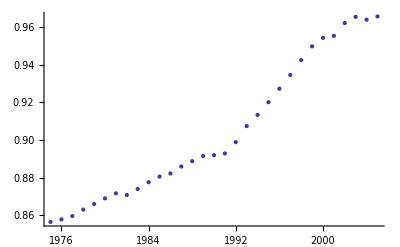

```mathematica
ListPlot[Table[{y, HDI["Australia", y]}, {y, 1975, 2005}]]
```

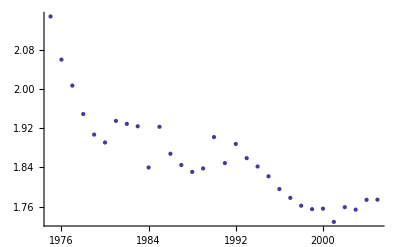

```mathematica
ListPlot[Table[{y, TFR["Australia", y]}, {y, 1975, 2005}]]
```

Generate the original plot reported in the paper

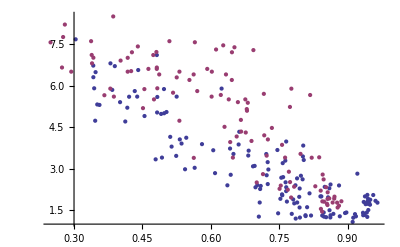

```mathematica
ListPlot[{
{HDI[#, 2005], TFR[#, 2005]}& /@ countrylist, 
{HDI[#, 1975], TFR[#, 1975]}& /@ countrylist} 
]
```

## Match Countries To Mathematica Country Data

Define an equivalent list of countries using Mathematica names by expanding some abbreviations and removing spaces

```mathematica
canonicallist = (countrylist /.{"USA" -> "UnitedStates", "Congo, Dem. Rep." -> "DemocraticRepublicCongo","Congo, Rep." -> "RepublicCongo", "Cote d'Ivoire" -> "IvoryCoast", "Kyrgyz Republic" -> "Kyrgyzstan", "NL" -> "Netherlands", "S. Korea" -> "SouthKorea", "Slovak Republic" -> "Slovakia", "Trinidad and Tobago" -> "TrinidadTobago",
"Lao" -> "Laos", x_String :> StringReplace[x, {" " -> ""}]});
```

Check that every country in the data matches one in Mathematica

```mathematica
Complement[canonicallist, CountryData["Countries"]]=={}
```

True

## Key Functions

Define (self-cacheing) function to map countries to the Mathematica names using the list

```mathematica
CanonicalName[country_String] :=
(CanonicalName[country] = canonicallist[[First[First[Position[countrylist, country]]]]])
```

Check this for three countries

```mathematica
CanonicalName /@ {"USA", "New Zealand", "United Kingdom"}
```

{UnitedStates,NewZealand,UnitedKingdom}

Get list of continents for countries

```mathematica
continentslist = Union[CountryData[CanonicalName[#], "Continent"]& /@ countrylist]
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to continents

```mathematica
ContinentOf[country_String] :=
(ContinentOf[country] = CountryData[CanonicalName[country], "Continent"])
```

Check this for four countries

```mathematica
ContinentOf /@ {"USA", "China", "Israel", "Australia"}
```

{NorthAmerica,Asia,Asia,Oceania}

Define ColourOf[] function from continents to colours by splitting the (reversed) DarkRainbow spectrum,
then display all values

```mathematica
MapThread[Set, {ColourOf /@ Reverse[continentslist], ColorData["DarkRainbow"]/@ (Range[Length[continentslist]]/Length[continentslist])}];
Style[#, FontColor -> ColourOf[#]]& /@ continentslist
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to their populations according to Mathematica

```mathematica
PopulationOf[country_String] :=
(PopulationOf[country] = CountryData[CanonicalName[country], "Population"])
```

Check this for four countries

```mathematica
PopulationOf /@ {"USA", "China", "Israel", "Australia"}
```

{3.02841×10^8,1.29801×10^9,6.80999×10^6,2.05304×10^7}

## Charts

Define function to plot a bubble chart of Total Fertility Rate against Human Development Index for a given year.  Bubble sizes are determined by population, colours by continent.

```mathematica
MyChart[year_Integer] :=
BubbleChart[{
(* Ensure legend appears in fixed order by "plotting" continents *)
Legended[Style[{0,0, 1}, ColourOf[#]], #]& /@ continentslist,
(* Add bubble for each country *) 
Legended[
Style[
(* On mouse-over, display country names *)
Tooltip[
{HDI[#, year], TFR[#, year], PopulationOf[#]},
#],
ColourOf[ContinentOf[#]]
],
ContinentOf[#]]& /@ countrylist},
BubbleSizes -> {0.01, 0.15}, PlotRange -> {{0.2, 1.0}, {0.8, 9}}, FrameLabel -> {"Human Development Index", "Total Fertility Rate"}, PlotLabel -> ToString[year]
]
```

Check this for one year

```mathematica
MyChart[1980]
```

-Graphics--Graphics- | Africa
-Graphics- | Asia
-Graphics- | Europe
-Graphics- | NorthAmerica
-Graphics- | Oceania
-Graphics- | SouthAmerica

Generate an animated GIF of all thirty years 
(Note: mouse-over will no work outside Mathematica)

```mathematica
Export["FertilityAndDevelopment.gif", Table[MyChart[y], {y, 1975, 2005, 1}]]
```

Use Mathematica's built in dynamic graphics to view animation

```mathematica
Manipulate[
MyChart[y],
{y, 1975, 2005, 1}]
```